```mathematica
d[n_,k_]:=Sum[d[j,k-1] d[n/j,1],{j,Divisors[n]}];d[n_,1]:=1;d[n_,0]:=0;d[1,0]:=1


tk1[n_,k_, a_]:= tk1[n,k,a]=Sum[ tk1[n/j,k-1,a],{j,1,n}]-a Sum[ tk1[n/(a j),k-1,a],{j,1,n/a}];tk1[n_,0,a_]:=1
```

```mathematica
EtoD[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j tk1[n/(b^j), k,b],{j,0,Log[b,n]}]
EtoDrng[n_, k_, b_,s1_,s2_] := Sum[ Binomial[k+j-1,k-1] b^j tk1[n/(b^j), k,b],{j,s1,s2}]
```

```mathematica
EtoD[8,1,1.01]
```

8.

```mathematica
tk1[100,3,.99]
```

35.5197

```mathematica
d[6,4]
```

16

```mathematica
N[8/7]
```

1.14286

```mathematica
N[8/6]
```

1.33333

```mathematica
N[d[6,2]]
```

4.

```mathematica
-1017.3949585738334+1019.3768024692354

-5116.0704331293155+5119.87203322637
```

1.98184

3.8016

```mathematica
Sum[ 8/n,{n,1,8}]
```

```mathematica
N[761/35]
```

```mathematica
21.742857142857144-8
```

13.7429

```mathematica
Table[ {j,b^j,Binomial[k+j-1,k-1] b^j tk1[n/(b^j), k,b]},{j,0,N[Log[b,n]]}]/.{b->1.0003,n->8,k->1}//TableForm
```

Table::iterb: Iterator {j, 0, Log[n]/Log[b]} does not have appropriate bounds.

```mathematica
Sum[ Binomial[1+j-1,1-1] b^j tk1[n/(b^j), k,b],{j,1,444}]/.{b->1.0003,n->8,k->1}
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

$Aborted

```mathematica
EtoDrng[8,1,1.0003,1,444]
```

-0.997489

```mathematica
EtoDrng[8,1,1.0003,446,958]
```

-1.14095

```mathematica
EtoDrng[8,1,1.0003,960,1565]
```

-1.32931

```mathematica
EtoDrng[8,2,1.0003,1,443]
EtoDrng[8,2,1.0003,444,445]
EtoDrng[8,2,1.0003,446,957]
EtoDrng[8,2,1.0003,958,959]
EtoDrng[8,2,1.0003,960,1564]
EtoDrng[8,2,1.0003,1565,1566]
```

0.15551

1.98184

0.565103

3.8016

1.01281

1.70023

```mathematica
Table[ {j,b^j,Binomial[k+j-1,k-1] b^j tk1[n/(b^j), k,b]},{j,0,N[Log[b,n]]}]/.{b->1.0003,n->8,k->2}//TableForm
```

Table::iterb: Iterator {j, 0, Log[n]/Log[b]} does not have appropriate bounds.

```mathematica
eee:=1.00001
nnn:=7
kk:=2
EtoDrng[nnn,kk,eee,0,1]
EtoDrng[nnn,kk,eee,1,Log[eee,nnn/(nnn-1)]-4]
EtoDrng[nnn,kk,eee,Log[eee,nnn/(nnn-1)]-4,Log[eee,nnn/(nnn-1)]+4]
EtoDrng[nnn,kk,eee,Log[eee,nnn/(nnn-1)]+4,Log[eee,nnn/(nnn-2)]-4]
EtoDrng[nnn,kk,eee,Log[eee,nnn/(nnn-2)]-4,Log[eee,nnn/(nnn-2)]+4]
EtoDrng[nnn,kk,eee,Log[eee,nnn/(nnn-2)]+4,Log[eee,nnn/(nnn-3)]-4]
EtoDrng[nnn,kk,eee,Log[eee,nnn/(nnn-3)]-4,Log[eee,nnn/(nnn-3)]+4]
EtoDrng[nnn,kk,eee,Log[eee,nnn/(nnn-3)]+4,Log[eee,nnn/(nnn-4)]-4]
EtoDrng[nnn,kk,eee,Log[eee,nnn/(nnn-4)]-4,Log[eee,nnn/(nnn-4)]+4]
EtoDrng[nnn,kk,eee,Log[eee,nnn/(nnn-4)]+4,Log[eee,nnn/(nnn-5)]-4]
EtoDrng[nnn,kk,eee,Log[eee,nnn/(nnn-5)]-4,Log[eee,nnn/(nnn-5)]+4]
EtoDrng[nnn,kk,eee,Log[eee,nnn/(nnn-5)]+4,Log[eee,nnn/(nnn-6)]-4]
EtoDrng[nnn,kk,eee,Log[eee,nnn/(nnn-6)]-4,Log[eee,nnn/(nnn-6)]+4]
```

2.

0.184395

3.94748

0.578643

1.85825

1.26573

2.31256

2.07133

0.713282

3.72224

-1.76864

5.73615

-6.62089

```mathematica
Table[ {j,b^j,Binomial[k+j-1,k-1] b^j tk1[n/(b^j), k,b]},{j,0,N[Log[b,n]]}]/.{b->1.0003,n->7,k->5}//TableForm
```

Table::iterb: Iterator {j, 0, Log[n]/Log[b]} does not have appropriate bounds.

```mathematica
-3.183930510163859*^11+9.555254625672328*^11+-9.558718486195774*^11+3.1873943706677026*^11
```

-1.96021

DiscretePlot::iterb: Iterator {j, 0, Log[b, n]} does not have appropriate bounds.

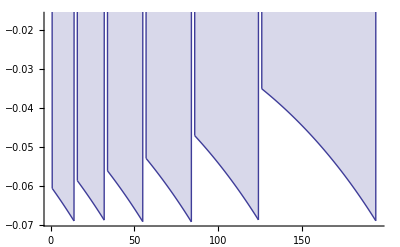

```mathematica
DiscretePlot[ Binomial[k+j-1,k-1] b^j tk1[n/(b^j), k,b],{j,0,Log[b,n]}]/.{k->1,n->7,b->1.01}
```

DiscretePlot::iterb: Iterator {j, 0, Log[b, n]} does not have appropriate bounds.

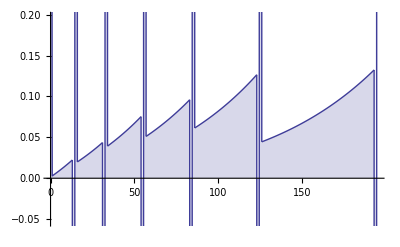

```mathematica
DiscretePlot[ Binomial[k+j-1,k-1] b^j tk1[n/(b^j), k,b],{j,0,Log[b,n]}]/.{k->2,n->7,b->1.01}
```

DiscretePlot::iterb: Iterator {j, 0, Log[b, n]} does not have appropriate bounds.

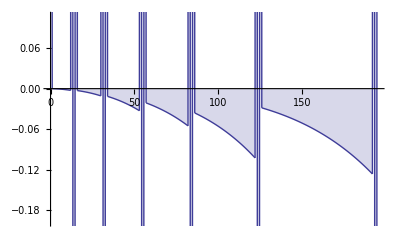

```mathematica
DiscretePlot[ Binomial[k+j-1,k-1] b^j tk1[n/(b^j), k,b],{j,0,Log[b,n]}]/.{k->3,n->7,b->1.01}
```

DiscretePlot::iterb: Iterator {j, 0, Log[b, n]} does not have appropriate bounds.

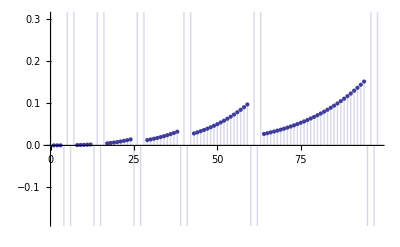

```mathematica
DiscretePlot[ Binomial[k+j-1,k-1] b^j tk1[n/(b^j), k,b],{j,0,Log[b,n]}]/.{k->4,n->7,b->1.02}
```